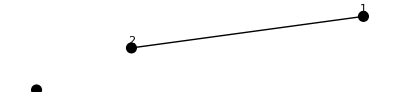

Левее

```mathematica
(*1*)
p1 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]};
p2 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]};
p0 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]};
p={p1,p2};
det = Det[{p2-p1, p0-p1}] ;
Graphics[{PointSize[0.02],Line[p],Point[p0],Point/@p,MapIndexed[Text[#2[[1]],#1+{0,.7}]&,p]}]
If[det> 0, "Левее", If[det < 0, "Правее", "Лежит на прямой"]]
```

{-13,3}

{-19,11}

{-1,15}

{6,-18}

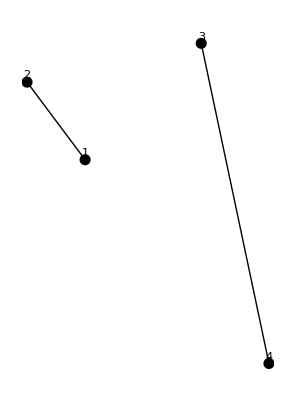

не пересекается

```mathematica
(*2*)
p1 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]}
p2 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]}
p3 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]}
p4 = {RandomInteger[{-20,20}],RandomInteger[{-20,20}]}
pp1={p1,p2};
pp2 = {p3, p4};
det1 = Det[{p4-p3, p1-p3}] ;
det2 = Det[{p4-p3, p2-p3}] ;
det3 = Det[{p2-p1, p3-p1}] ;
det4 = Det[{p2-p1, p4-p1}] ;
Graphics[{PointSize[0.02],Line[pp1],Line[pp2],Point/@pp1,Point/@pp2,MapIndexed[Text[#2[[1]],#1+{0,.7}]&,pp1],MapIndexed[Text[#2[[1]]+2,
#1+{0,.7}]&,pp2]}]
If[det1==0&& det2==0&& det3==0&& det4==0, If[(p3[[1]]-p1[[1]])*(p4[[1]]-p1[[1]])+(p3[[2]]-p1[[2]])*(p4[[2]]-p1[[2]])≤0||(p3[[1]]-p2[[1]])*(p4[[1]]-p2[[1]])+(p3[[2]]-p2[[2]])*(p4[[2]]-p2[[2]])≤0||(p2[[1]]-p3[[1]])*(p1[[1]]-p3[[1]])+(p2[[2]]-p3[[2]])*(p1[[2]]-p3[[2]])≤0||(p2[[1]]-p4[[1]])*(p1[[1]]-p4[[1]])+(p2[[2]]-p4[[2]])*(p1[[2]]-p4[[2]])≤0,"пересекается","не пересекается"],If[det1*det2<=0&& det3*det4<=0,"пересекается","не пересекается"]]
```

```mathematica
(*3*)
```

5

{{-16,-15},{19,11},{11,-15},{-20,-16},{-13,-5}}

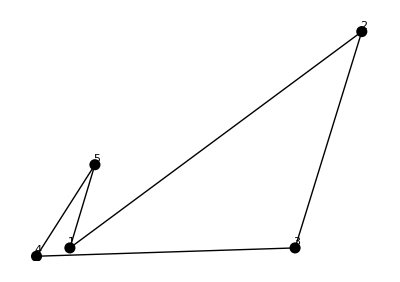

Простой

```mathematica
n=RandomInteger[{3,15}]
a=0;
P=Table[{RandomInteger[{-20,20}],RandomInteger[{-20,20}]},{n}]
Graphics[{Line[Append[P,P[[1]]]],PointSize[0.02],Point/@P, MapIndexed[Text[#2[[1]],#1+{.2,.7}]&,P]}]

For[i=1,i≤n-2,i++,For[j=i+2,j≤n,j++,{
If[j==n&&i≠n,{
det1 = Det[{P[[1]]-P[[j]], P[[i]]-P[[j]]}] ;
det2 = Det[{P[[1]]-P[[j]], P[[i+1]]-P[[j]]}]; 
det3 = Det[{P[[i+1]]-P[[i]], P[[j]]-P[[i]]}] ;
det4 = Det[{P[[i+1]]-P[[i]], P[[1]]-P[[i]]}]; 
If[det1==0&& det2==0&& det3==0&& det4==0, If[(P[[j]][[1]]-P[[i]][[1]])*(P[[1]][[1]]-P[[i]][[1]])+(P[[j]][[2]]-P[[i]][[2]])*(P[[1]][[2]]-P[[i]][[2]])≤0||(P[[j]][[1]]-P[[i+1]][[1]])*(P[[1]][[1]]-P[[i+1]][[1]])+(P[[j]][[2]]-P[[i+1]][[2]])*(P[[1]][[2]]-P[[i+1]][[2]])≤0||(P[[i+1]][[1]]-P[[j]][[1]])*(P[[i]][[1]]-P[[j]][[1]])+(P[[i+1]][[2]]-P[[j]][[2]])*(P[[i]][[2]]-P[[j]][[2]])≤0||(P[[i+1]][[1]]-P[[1]][[1]])*(P[[i]][[1]]-P[[1]][[1]])+(P[[i+1]][[2]]-P[[1]][[2]])*(P[[i]][[2]]-P[[1]][[2]])≤0,a++,a=a],If[det1*det2<0&& det3*det4<0, a++]]}];

If[i≠n&&j≠n,{
det1 = Det[{P[[j+1]]-P[[j]], P[[i]]-P[[j]]}] ;
det2 = Det[{P[[j+1]]-P[[j]], P[[i+1]]-P[[j]]}]; 
det3 = Det[{P[[i+1]]-P[[i]], P[[j]]-P[[i]]}] ;
det4 = Det[{P[[i+1]]-P[[i]], P[[j+1]]-P[[i]]}]; 
If[det1==0&& det2==0&& det3==0&& det4==0, If[(P[[j]][[1]]-P[[i]][[1]])*(P[[j+1]][[1]]-P[[i]][[1]])+(P[[j]][[2]]-P[[i]][[2]])*(P[[j+1]][[2]]-P[[i]][[2]])≤0||(P[[j]][[1]]-P[[i+1]][[1]])*(P[[j+1]][[1]]-P[[i+1]][[1]])+(P[[j]][[2]]-P[[i+1]][[2]])*(P[[j+1]][[2]]-P[[i+1]][[2]])≤0||(P[[i+1]][[1]]-P[[j]][[1]])*(P[[i]][[1]]-P[[j]][[1]])+(P[[i+1]][[2]]-P[[j]][[2]])*(P[[i]][[2]]-P[[j]][[2]])≤0||(P[[i+1]][[1]]-P[[j+1]][[1]])*(P[[i]][[1]]-P[[j+1]][[1]])+(P[[i+1]][[2]]-P[[j+1]][[2]])*(P[[i]][[2]]-P[[j+1]][[2]])≤0,a++,a=a],If[det1*det2<0&& det3*det4<0, a++]]}];

}]]
If[a>0,"Не простой", "Простой"]
```